Solve equations for the probabilities of the cluster containing 0, 1 or 2 labeled molecules.

```mathematica
Flatten[FullSimplify[soln =DSolve[{p0'[t]==-kon p0[t],p1'[t]==kon p0[t]+2*koff p2[t] -(kon+koff) p1[t],p2'[t] ==kon p1[t]-(kon+2*koff) p2[t],p0[0]==1,p1[0]==0,p2[0]==0},{p0[t], p1[t],p2[t]},t]]];
```

Probability density for a successful binding/unbinding event occurring at time t.

```mathematica
f1 =koff p1[t]/.soln;
```

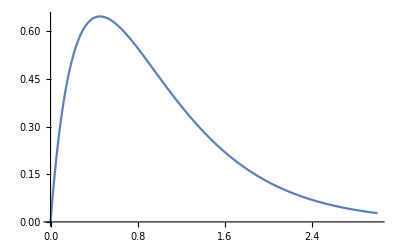

```mathematica
Plot[{f1/.{kon->1.65,koff->2.67}},{t,0,3}]
```

Probability that a successful binding/unbinding event occurs.

```mathematica
soln3 = Integrate[f1,{t,0,Infinity}]
```

{ConditionalExpression[(koff (2 koff+kon))/(2 koff^2+koff kon+kon^2),Re[√koff √(koff+8 kon)]<kon+Conjugate[kon]+3 Re[koff]&&kon>0&&Re[3 koff+2 kon+√koff √(koff+8 kon)]>0]}

```mathematica
ps =(koff (2 koff+kon))/(2 koff^2+koff kon+kon^2);
```

Probability density for a third labeled molecule binding at time t.

```mathematica
f2 =kon p2[t]/.soln;
```

Probability that a third labeled molecule binds.

```mathematica
Integrate[f2,{t,0,Infinity}]
```

{ConditionalExpression[kon^2/(2 koff^2+koff kon+kon^2),Re[√koff √(koff+8 kon)]<kon+Conjugate[kon]+3 Re[koff]&&kon>0&&Re[3 koff+2 kon+√koff √(koff+8 kon)]>0]}

```mathematica
pf = kon^2/(2 koff^2+koff kon+kon^2);
```

Check probabilities sum to 1.

```mathematica
FullSimplify[ps+pf]
```

1

Probability density for cluster disassembly.

```mathematica
f3 = klt  Exp[(-klt t2)];
```

```mathematica
fj1=f1*f3;
```

Probability density for a successful binding/unbinding event occurring at time t when cluster disassembly is considered.

```mathematica
fpt = Integrate[fj1,{t2,t,Infinity}]
```

{ConditionalExpression[-1/(2 (koff^2+7 koff kon-8 kon^2))ⅇ^(-1/2 (2 klt+3 koff+2 kon+√koff √(koff+8 kon)) t) √koff kon ((1+ⅇ^(√koff √(koff+8 kon) t)-2 ⅇ^(1/2 (3 koff t+√koff √(koff+8 kon) t))) koff^(3/2)+8 (1+ⅇ^(√koff √(koff+8 kon) t)-2 ⅇ^(1/2 (3 koff t+√koff √(koff+8 kon) t))) √koff kon+(-1+ⅇ^(√koff √(koff+8 kon) t)) koff √(koff+8 kon)+2 (-1+ⅇ^(√koff √(koff+8 kon) t)) kon √(koff+8 kon)),Re[klt]>0]}

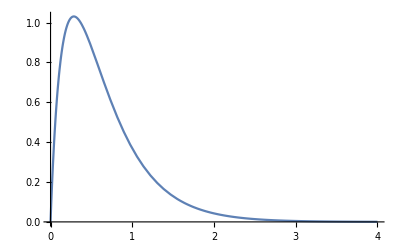

```mathematica
Plot[fpt/.{kon->2.2,koff->5.1,klt->0.049},{t,0,4}]
```

Probability of a successful binding/unbinding event (Eq. 1 of Methods).

```mathematica
Integrate[fj1,{t,0,Infinity},{t2,t,Infinity}]
```

{ConditionalExpression[(koff kon (klt+2 koff+kon))/((klt+kon) (klt^2+3 klt koff+2 koff^2+2 klt kon+koff kon+kon^2)),Re[klt+kon]>0&&Re[2 klt+3 koff+2 kon-√koff √(koff+8 kon)]>0&&Re[klt+(3 koff)/2+kon+1/2 √koff √(koff+8 kon)]>0]}

```mathematica
psuc =(koff kon (klt+2 koff+kon))/((klt+kon) (klt^2+3 klt koff+2 koff^2+2 klt kon+koff kon+kon^2));
```

Compute average time for a successful binding/unbinding event (Tavg in Methods).

```mathematica
Integrate[t*fpt/psuc,{t,0,Infinity}]
```

{ConditionalExpression[((2 klt+koff) (klt+2 koff)^2+2 (3 klt^2+9 klt koff+4 koff^2) kon+3 (2 klt+3 koff) kon^2+2 kon^3)/((klt+kon) (klt+2 koff+kon) (klt^2+3 klt koff+2 koff^2+2 klt kon+koff kon+kon^2)),Re[klt]>0&&klt+kon>0&&klt+kon+Conjugate[klt]+Conjugate[kon]+3 Re[koff]>Re[√koff √(koff+8 kon)]&&Re[klt+(3 koff)/2+kon+1/2 √koff √(koff+8 kon)]>0]}

```mathematica
mfpt = ((koff-kon) (koff+8 kon) ((2 klt+koff) (klt+2 koff)^2+2 (3 klt^2+9 klt koff+4 koff^2) kon+3 (2 klt+3 koff) kon^2+2 kon^3))/((klt+kon) (klt+2 koff+kon) (koff^2+7 koff kon-8 kon^2) (klt^2+3 klt koff+2 koff^2+2 klt kon+koff kon+kon^2));
```

```mathematica
mfpt2 = ((2 klt+koff) (klt+2 koff)^2+2 (3 klt^2+9 klt koff+4 koff^2) kon+3 (2 klt+3 koff) kon^2+2 kon^3)/((klt+kon) (klt+2 koff+kon) (klt^2+3 klt koff+2 koff^2+2 klt kon+koff kon+kon^2));
```

```mathematica
Simplify[mfpt == mfpt2]
```

True

Numerically solve for koff and klt given kon, psuc and mfpt.

```mathematica
params = { kon-> 2.4, psucn->0.9,mfptn->0.62};
```

```mathematica
eqn4 = psucn== psuc/. params;
```

```mathematica
eqn3 = mfptn == mfpt /. params;
```

```mathematica
NSolve[{eqn3,eqn4} ,{koff,klt}]
```

{{klt→27.0154,koff→-18.0321},{klt→27.0154,koff→-18.0321},{klt→-0.831509,koff→-2.63789},{klt→0.0288695,koff→5.04838}}

Probability of failure because a third labeled molecule arrives before disassembly.

```mathematica
fj2 = f2*f3;
```

```mathematica
Integrate[fj2,{t,0,Infinity},{t2,t,Infinity}]
```

{ConditionalExpression[kon^3/((klt+kon) (klt^2+3 klt koff+2 koff^2+2 klt kon+koff kon+kon^2)),Re[klt+kon]>0&&Re[2 klt+3 koff+2 kon-√koff √(koff+8 kon)]>0&&Re[klt+(3 koff)/2+kon+1/2 √koff √(koff+8 kon)]>0]}

```mathematica
pf1 = kon^3/((klt+kon) (klt^2+3 klt koff+2 koff^2+2 klt kon+koff kon+kon^2));
```

Probability of failure because  the cluster disassembles.

```mathematica
Integrate[fj2+fj1,{t2,0,Infinity},{t,t2,Infinity}]
```

{ConditionalExpression[(klt (klt^2+2 koff^2+3 koff kon+3 kon^2+3 klt (koff+kon)))/((klt+kon) (klt^2+3 klt koff+2 koff^2+2 klt kon+koff kon+kon^2)),klt+kon>0&&klt+kon+Conjugate[klt]+Conjugate[kon]+3 Re[koff]>Re[√koff √(koff+8 kon)]&&Re[klt+(3 koff)/2+kon+1/2 √koff √(koff+8 kon)]>0]}

```mathematica
pf2 = (klt (klt^2+2 koff^2+3 koff kon+3 kon^2+3 klt (koff+kon)))/((klt+kon) (klt^2+3 klt koff+2 koff^2+2 klt kon+koff kon+kon^2));
```

Verify probabilities sum to 1.

```mathematica
Simplify[pf1+pf2 +psuc]
```

1

```mathematica
params2 = {kon-> 2.4,koff->5.04838,klt->0.0288695};
```

```mathematica
pp2 =pf2 /.params2;
```

```mathematica
pp3 =psuc/.params2;
```

```mathematica
pp =pf1 /. params2;
```

Fraction of successfully identified clusters.

```mathematica
psi =pp2*Sum[pp3^n ,{n,10,Infinity}];
```

0.062828

Fraction that fail because 3 or more clusters are present simultaneously.

```mathematica
p2t = pp*Sum[pp3^n ,{n,0,Infinity}]
```

0.819811

Fraction that don’t reach minimum of 10 successful binding/unbinding events.

```mathematica
pf10 =pp2*Sum[pp3^n ,{n,0,9}]
```

0.117361

Verify probabilities sum to one.

```mathematica
psi+p2t+pf10
```

1.